## Bulk part of open system

Nx * Ny cylinder. Boundary at positions y=0,Ny-1. Set period T=2.5π. Special value of J is J=1. Nx, Ny and thickness are only even

```mathematica
Nx=20;
Ny=40;
thickness=16;
J=1;
W=.
n=5000;
α=.
λ=0.1;
Bi=(2 π)/(n Nx Ny)0.00001
```

1.5708×10^-11

```mathematica
1/2-1/2 Tanh[α/2]//N
```

0.5

```mathematica
0.172103
```

rectify 2D coordinates by defining 1D index i=Ny Mod[x,Nx]+y (below, Mod[x,Nx] is due to periodicity in x). Hence, y=Mod[i,Ny], x=(i-Mod[i,Ny])/Ny

```mathematica
Pr=DiagonalMatrix[Table[If[Mod[j,Ny]< Ny/2-thickness/2|| Mod[j,Ny]>Ny/2+thickness/2-1,0,1],{j,0,Ny Nx-1}]];
Id=DiagonalMatrix[Table[1,{i,0,Nx Ny-1}]];
```

```mathematica
Pot=DiagonalMatrix[Table[w[(i-Mod[i,Ny])/Ny,Mod[i,Ny]]+λ If[ Mod[(i-Mod[i,Ny])/Ny+Mod[i,Ny],2]==0,1,-1],{i,0,Nx Ny-1}]];
H1[B_]=-J Table[If[Ny==Mod[i-j, Nx Ny] &&  Mod[(j-Mod[j,Ny])/Ny+Mod[j,Ny],2]==0,E^(-I B Mod[j,Ny]),0]+   If[Ny==Mod[j-i,Nx Ny] &&  Mod[(i-Mod[i,Ny])/Ny+Mod[i,Ny],2]==0,E^(I B Mod[j,Ny]),0],{i,0,Nx Ny-1},{j,0,Nx Ny-1}]+Pot;
H2[B_]=-J Table[ If[1==Mod[i-j,Ny] &&  Mod[(j-Mod[j,Ny])/Ny+Mod[j,Ny] ,2]==0&& (j-Mod[j,Ny])/Ny==(i-Mod[i,Ny])/Ny&& Mod[j,Ny]≠Ny-1,1,0]+  If[1==Mod[j-i,Ny] &&  Mod[(i-Mod[i,Ny])/Ny+Mod[i,Ny],2]==0&& (j-Mod[j,Ny])/Ny==(i-Mod[i,Ny])/Ny&&  Mod[j,Ny]≠0,1,0],{i,0,Nx Ny-1},{j,0,Nx Ny-1}]+Pot;
H3[B_]=-J Table[ If[Ny==Mod[j-i,Nx Ny] &&  Mod[(j-Mod[j,Ny])/Ny+Mod[j,Ny],2]==0,E^(I B Mod[j,Ny]),0]+  If[Ny==Mod[i-j,Nx Ny] &&  Mod[(i-Mod[i,Ny])/Ny+Mod[i,Ny],2]==0,E^(-I B Mod[j,Ny]),0],{i,0,Nx Ny-1},{j,0,Nx Ny-1}]+Pot;
H4[B_]=-J Table[ If[1==Mod[j-i,Ny] &&  Mod[(j-Mod[j,Ny])/Ny+Mod[j,Ny] ,2]==0&& (j-Mod[j,Ny])/Ny==(i-Mod[i,Ny])/Ny&& Mod[j,Ny]≠0,1,0]+  If[1==Mod[i-j,Ny] &&  Mod[(i-Mod[i,Ny])/Ny+Mod[i,Ny],2]==0&& (j-Mod[j,Ny])/Ny==(i-Mod[i,Ny])/Ny&& Mod[j,Ny]≠Ny-1,1,0],{i,0,Nx Ny-1},{j,0,Nx Ny-1}]+Pot;
H5=Pot;
```

## λ=0 Nx=20, Ny=40, thickness=16

#### α=0

```mathematica
Table[Table[w[i,j]= RandomReal[{-0,0}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,1}]
Sum[s[p],{p,1,5}]/5
```

{-4.36152×10^-6-0.5 ⅈ}

1/5 ((-4.36152×10^-6-0.5 ⅈ)+s[2]+s[3]+s[4]+s[5])

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1,1}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
```

{0.0000103765-0.499613 ⅈ,-9.12316×10^-6-0.499612 ⅈ,0.0000125533-0.499395 ⅈ,-2.0829×10^-6-0.499447 ⅈ,2.16588×10^-6-0.499654 ⅈ,0.0000125982-0.499232 ⅈ,0.0000114193-0.497507 ⅈ,2.78982×10^-6-0.496975 ⅈ,-0.0000104669-0.499852 ⅈ,-9.11472×10^-7-0.499878 ⅈ,0.000011688-0.499699 ⅈ,-0.0000135704-0.499907 ⅈ,1.28599×10^-6-0.499196 ⅈ,-0.0000194191-0.499831 ⅈ,0.0000128582-0.494238 ⅈ,2.47745×10^-6-0.49778 ⅈ,4.8884×10^-6-0.499465 ⅈ,-3.12135×10^-6-0.499238 ⅈ,-5.24448×10^-6-0.498975 ⅈ,0.0000124318-0.499961 ⅈ}

1.67965×10^-6-0.498973 ⅈ

```mathematica
s1=-Im[%]
```

```mathematica
s1a=0.3701362024485271
```

0.370136

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0.3,0.3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s03=-Im[%]
```

{-4.51379×10^-6-0.499937 ⅈ,6.42982×10^-6-0.500026 ⅈ,-0.0000181754-0.499957 ⅈ,8.90851×10^-6-0.500053 ⅈ,-4.78519×10^-6-0.499971 ⅈ,-2.17495×10^-6-0.499894 ⅈ,6.05878×10^-7-0.500019 ⅈ,9.26513×10^-8-0.500055 ⅈ,0.0000128379-0.500044 ⅈ,-0.0000181776-0.50004 ⅈ,-7.16717×10^-6-0.499949 ⅈ,0.0000158878-0.499957 ⅈ,5.07462×10^-6-0.500047 ⅈ,-0.000014006-0.499994 ⅈ,-8.06194×10^-6-0.500045 ⅈ,3.8534×10^-6-0.499962 ⅈ,-7.46338×10^-6-0.499865 ⅈ,3.35329×10^-6-0.500008 ⅈ,-0.0000144991-0.50001 ⅈ,7.82747×10^-6-0.500024 ⅈ}

-1.70766×10^-6-0.499993 ⅈ

0.499993

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1.3,1.3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s13=-Im[%]
```

{-0.0000186314-0.463868 ⅈ,2.94547×10^-6-0.479921 ⅈ,-0.0000163196-0.475039 ⅈ,-2.46238×10^-6-0.476149 ⅈ,-0.0000202112-0.496993 ⅈ,-0.0000195515-0.486476 ⅈ,-0.0000167744-0.494639 ⅈ,-0.0000159867-0.492745 ⅈ,-0.0000133763-0.480322 ⅈ,-0.0000156744-0.467315 ⅈ,8.50515×10^-6-0.493354 ⅈ,-0.0000179855-0.48599 ⅈ,-0.000018755-0.472148 ⅈ,-0.00001356-0.473776 ⅈ,0.0000102344-0.48498 ⅈ,8.45497×10^-7-0.484778 ⅈ,-4.74705×10^-6-0.486225 ⅈ,-0.0000174959-0.479889 ⅈ,-0.000019157-0.464269 ⅈ,-7.06198×10^-6-0.483294 ⅈ}

-0.000010761-0.481108 ⅈ

0.481108

```mathematica
s13a=0.3440957959346258
```

0.344096

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1.7,1.7}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s17=-Im[%]
```

{-6.6319×10^-6-0.361165 ⅈ,-9.30571×10^-6-0.334054 ⅈ,8.28565×10^-6-0.401272 ⅈ,-1.54409×10^-6-0.396031 ⅈ,-6.89843×10^-6-0.369744 ⅈ,-2.12613×10^-6-0.360199 ⅈ,-0.0000109243-0.379261 ⅈ,0.0000128313-0.348539 ⅈ,-0.0000142242-0.392077 ⅈ,3.50964×10^-6-0.437145 ⅈ,1.80929×10^-6-0.40269 ⅈ,-0.0000178688-0.3906 ⅈ,-3.52586×10^-6-0.402216 ⅈ,0.00001436-0.444871 ⅈ,-1.45187×10^-6-0.375391 ⅈ,0.0000140779-0.376928 ⅈ,-0.0000184005-0.386563 ⅈ,-2.52806×10^-6-0.457959 ⅈ,7.40846×10^-6-0.390805 ⅈ,-4.82958×10^-6-0.304713 ⅈ}

-1.89886×10^-6-0.385611 ⅈ

0.385611

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-2,2}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s2=-Im[%]
```

{-0.0000119845-0.259962 ⅈ,-0.0000142733-0.208179 ⅈ,0.0000135309-0.251394 ⅈ,-8.08861×10^-6-0.213961 ⅈ,0.0000118747-0.335964 ⅈ,-7.61729×10^-6-0.262666 ⅈ,0.0000150675-0.204666 ⅈ,0.0000130446-0.187943 ⅈ,-4.88822×10^-6-0.252939 ⅈ,-8.31036×10^-6-0.263911 ⅈ,0.0000140834-0.180196 ⅈ,0.0000103323-0.252044 ⅈ,0.0000141158-0.230964 ⅈ,-0.0000106884-0.2445 ⅈ,9.61057×10^-6-0.208733 ⅈ,-2.52894×10^-6-0.320094 ⅈ,0.0000155822-0.263791 ⅈ,9.75645×10^-6-0.221156 ⅈ,-0.0000110785-0.297079 ⅈ,0.0000142219-0.282849 ⅈ}

3.08812×10^-6-0.24715 ⅈ

0.24715

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-2.5,2.5}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s06=-Im[%]
```

{2.97179×10^-7-0.200957 ⅈ,0.0000160983-0.0789077 ⅈ,-9.42699×10^-6-0.0884084 ⅈ,-9.42816×10^-6-0.0653014 ⅈ,-0.000014831-0.14907 ⅈ,2.05361×10^-6-0.166834 ⅈ,-0.0000123687-0.102716 ⅈ,8.27988×10^-6-0.0379986 ⅈ,-3.72491×10^-6-0.144781 ⅈ,0.0000187605-0.129496 ⅈ,0.0000169249-0.0429055 ⅈ,-3.24401×10^-6-0.0553417 ⅈ,0.0000114217-0.0981904 ⅈ,0.0000121322-0.0783386 ⅈ,-8.06623×10^-6-0.0698216 ⅈ,0.0000100513-0.127283 ⅈ,1.55233×10^-6-0.120846 ⅈ,0.0000122484-0.0419904 ⅈ,0.0000133978-0.110734 ⅈ,0.0000116114-0.113602 ⅈ}

3.68697×10^-6-0.101176 ⅈ

0.101176

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-3,3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s06=-Im[%]
```

{4.69328×10^-6-0.0292819 ⅈ,-8.55234×10^-6-0.027579 ⅈ,0.0000128825-0.037248 ⅈ,-0.000011756-0.0177858 ⅈ,8.86585×10^-6+0.000374267 ⅈ,-0.0000166604-0.0262088 ⅈ,-0.0000142831-0.00856473 ⅈ,0.000011428-0.0283266 ⅈ,-6.32032×10^-6-0.00489528 ⅈ,8.97083×10^-6-0.0394282 ⅈ,-2.46735×10^-6-0.0858677 ⅈ,-1.2736×10^-6-0.0207236 ⅈ,-0.0000110958-0.0388181 ⅈ,-0.0000174116-0.00982974 ⅈ,0.0000123517+0.0051325 ⅈ,0.0000110139-0.060396 ⅈ,0.0000102009-0.00447857 ⅈ,-4.60817×10^-6-0.00524575 ⅈ,-2.14608×10^-7-0.0278912 ⅈ,-0.0000125676-0.0681829 ⅈ}

-1.3402×10^-6-0.0267622 ⅈ

0.0267622

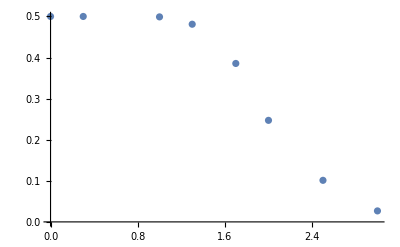

```mathematica
ListPlot[{{0,0.5},{0.3,0.49999280391359796},{1,0.49897266536987595},{1.3,0.48110840053714815},{1.7,0.3856111589029572},{2,0.2471495887755022},{2.5,0.1011762112242147},{3,0.02676224398527608}}]
```

#### α=π/3

```mathematica
α=π/3;
λ=0;
```

```mathematica
1/2-1/2 Tanh[α/2]//N
```

0.259764

```mathematica
Table[Table[w[i,j]= RandomReal[{-0,0}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,1}]
Sum[s[p],{p,1,1}]/1
```

{-8.53754×10^-7-0.259764 ⅈ}

-8.53754×10^-7-0.259764 ⅈ

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1,1}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
```

{8.00592×10^-6-0.258885 ⅈ,-5.97165×10^-6-0.259224 ⅈ,-8.43966×10^-6-0.258911 ⅈ,5.84999×10^-6-0.258972 ⅈ,-3.84455×10^-6-0.259036 ⅈ,-8.23688×10^-6-0.258818 ⅈ,4.3074×10^-6-0.258535 ⅈ,7.51331×10^-6-0.259399 ⅈ,-9.13592×10^-6-0.25962 ⅈ,-3.61479×10^-6-0.25945 ⅈ,-9.23088×10^-6-0.259743 ⅈ,-3.88204×10^-7-0.25971 ⅈ,7.50122×10^-6-0.259646 ⅈ,-9.95742×10^-6-0.259044 ⅈ,3.50583×10^-6-0.259426 ⅈ,-3.43439×10^-6-0.259179 ⅈ,6.92093×10^-6-0.259636 ⅈ,-5.43927×10^-6-0.259464 ⅈ,-9.30136×10^-8-0.259392 ⅈ,8.25574×10^-6-0.259339 ⅈ}

-7.96314×10^-7-0.259272 ⅈ

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0.3,0.3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s03=-Im[%]
```

{1.34423×10^-6-0.259755 ⅈ,-5.18112×10^-6-0.259741 ⅈ,-6.21431×10^-6-0.258803 ⅈ,-1.05691×10^-6-0.259756 ⅈ,6.89575×10^-6-0.259743 ⅈ,4.36394×10^-6-0.259734 ⅈ,4.172×10^-6-0.259741 ⅈ,-7.12645×10^-6-0.259485 ⅈ,-1.5496×10^-6-0.259808 ⅈ,7.90451×10^-6-0.25977 ⅈ,3.04852×10^-6-0.259725 ⅈ,7.24441×10^-6-0.25976 ⅈ,-7.63903×10^-6-0.259728 ⅈ,5.46613×10^-6-0.259683 ⅈ,7.93567×10^-6-0.259782 ⅈ,2.09408×10^-6-0.259762 ⅈ,-7.4999×10^-6-0.259757 ⅈ,-1.90136×10^-6-0.259724 ⅈ,-0.0000106087-0.259768 ⅈ,1.61817×10^-6-0.259724 ⅈ}

1.65502×10^-7-0.259687 ⅈ

0.259687

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1.3,1.3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s13=-Im[%]
```

{8.80987×10^-7-0.248497 ⅈ,-9.90778×10^-7-0.253285 ⅈ,4.31925×10^-6-0.254667 ⅈ,4.00242×10^-6-0.251176 ⅈ,3.26802×10^-7-0.253835 ⅈ,7.03863×10^-6-0.256755 ⅈ,-7.46798×10^-6-0.248303 ⅈ,-9.55811×10^-6-0.25248 ⅈ,-2.49757×10^-6-0.24577 ⅈ,-5.29792×10^-6-0.248243 ⅈ,2.46629×10^-6-0.246003 ⅈ,-4.54659×10^-6-0.24427 ⅈ,4.22886×10^-6-0.254067 ⅈ,6.33465×10^-6-0.245969 ⅈ,3.47564×10^-8-0.250565 ⅈ,4.14367×10^-6-0.255512 ⅈ,-9.72821×10^-6-0.256336 ⅈ,5.41283×10^-6-0.255984 ⅈ,-4.92485×10^-6-0.255355 ⅈ,-0.0000101817-0.255955 ⅈ}

-8.0023×10^-7-0.251651 ⅈ

0.251651

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1.7,1.7}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s17=-Im[%]
```

{-7.39964×10^-6-0.192269 ⅈ,5.27559×10^-6-0.191553 ⅈ,5.60484×10^-8-0.179701 ⅈ,-7.06621×10^-6-0.1805 ⅈ,-3.02806×10^-6-0.165655 ⅈ,-6.30802×10^-6-0.199698 ⅈ,6.4277×10^-6-0.20102 ⅈ,-5.99377×10^-6-0.177815 ⅈ,-1.77705×10^-6-0.201615 ⅈ,4.30002×10^-7-0.202376 ⅈ,-6.21704×10^-6-0.221666 ⅈ,-8.178×10^-7-0.186637 ⅈ,3.74107×10^-6-0.211395 ⅈ,-6.36315×10^-6-0.187515 ⅈ,-1.98716×10^-6-0.211042 ⅈ,1.10898×10^-6-0.198775 ⅈ,-6.61732×10^-6-0.225704 ⅈ,-5.36611×10^-6-0.184381 ⅈ,6.18697×10^-7-0.221066 ⅈ,-4.05076×10^-6-0.21909 ⅈ}

-2.2667×10^-6-0.197974 ⅈ

0.197974

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-2,2}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s2=-Im[%]
```

{-4.68905×10^-6-0.126345 ⅈ,2.26856×10^-6-0.13716 ⅈ,1.4183×10^-6-0.122679 ⅈ,-7.81699×10^-6-0.111719 ⅈ,4.94808×10^-6-0.178288 ⅈ,-8.40815×10^-6-0.132195 ⅈ,6.42499×10^-6-0.153996 ⅈ,-4.11506×10^-7-0.119416 ⅈ,-1.81364×10^-6-0.147743 ⅈ,3.56276×10^-6-0.135314 ⅈ,2.25887×10^-6-0.17505 ⅈ,7.84947×10^-6-0.177458 ⅈ,7.4892×10^-6-0.167281 ⅈ,9.15478×10^-7-0.0909309 ⅈ,8.69571×10^-6-0.150847 ⅈ,-3.85747×10^-6-0.137731 ⅈ,-1.01027×10^-7-0.13029 ⅈ,-5.38783×10^-6-0.155006 ⅈ,3.91838×10^-6-0.141187 ⅈ,-9.52377×10^-7-0.134622 ⅈ}

8.15587×10^-7-0.141263 ⅈ

0.141263

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-2.5,2.5}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s06=-Im[%]
```

{1.87479×10^-6-0.0768733 ⅈ,6.57734×10^-6-0.0502887 ⅈ,-6.59164×10^-6-0.0575867 ⅈ,-2.31147×10^-6-0.0356548 ⅈ,-3.33692×10^-6-0.0793117 ⅈ,-6.10419×10^-6-0.0781861 ⅈ,-9.05281×10^-6-0.0865725 ⅈ,-4.31705×10^-6-0.0205452 ⅈ,7.49436×10^-7-0.0408762 ⅈ,3.11307×10^-6-0.0257403 ⅈ,8.23983×10^-6-0.0716803 ⅈ,-4.44824×10^-6-0.107617 ⅈ,-4.85945×10^-6-0.0419238 ⅈ,-4.19709×10^-6-0.0412528 ⅈ,7.00509×10^-6-0.0267135 ⅈ,-5.37265×10^-6-0.0711839 ⅈ,6.01506×10^-6-0.0644819 ⅈ,4.26702×10^-6-0.0333664 ⅈ,3.59846×10^-6-0.0285131 ⅈ,6.74837×10^-6-0.00510082 ⅈ}

-1.20153×10^-7-0.0521735 ⅈ

0.0521735

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-3,3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s06=-Im[%]
```

{4.49307×10^-6-0.0129774 ⅈ,4.78497×10^-6-0.0353292 ⅈ,6.5233×10^-6-0.00917925 ⅈ,7.36028×10^-6-0.010447 ⅈ,8.1158×10^-6-0.0137516 ⅈ,2.17728×10^-6-0.00747141 ⅈ,6.58253×10^-6-0.0178819 ⅈ,-3.76947×10^-6+0.00231955 ⅈ,-3.16135×10^-6-0.0180068 ⅈ,-8.94537×10^-6-0.0243894 ⅈ,-3.38437×10^-6-0.0239961 ⅈ,-4.96983×10^-6-0.0274645 ⅈ,2.42038×10^-6-0.000771077 ⅈ,-2.81292×10^-6-0.0218784 ⅈ,3.21123×10^-6-0.0234241 ⅈ,-3.29573×10^-6-0.0312978 ⅈ,7.70223×10^-6-0.00152374 ⅈ,-4.09134×10^-6+0.00998331 ⅈ,3.03999×10^-7-0.00456751 ⅈ,3.70367×10^-7-0.0142024 ⅈ}

9.80753×10^-7-0.0143128 ⅈ

0.0143128

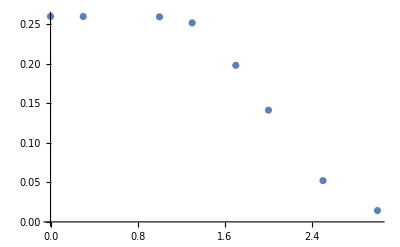

```mathematica
ListPlot[{{0,0.25976361091989103},{0.3,0.25968744711606145},{1,0.2592715233139963},{1.3,0.2516513965790576},{1.7,0.19797365318528562},{2,0.14126280061004318},{2.5,0.05217346333835901},{3,0.01431283694396155}}]
```

## λ=0.1 Nx=20, Ny=40, thickness=16

#### α=0

```mathematica
α=0;
λ=0.1;
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0,0}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,1}]
Sum[s[p],{p,1,1}]/1
```

{-0.0000283304-0.485239 ⅈ}

-0.0000283304-0.485239 ⅈ

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0.3,0.3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
```

{-0.0000106193-0.499824 ⅈ,-7.43455×10^-6-0.499586 ⅈ,-3.77603×10^-6-0.500002 ⅈ,3.78743×10^-6-0.500042 ⅈ,-0.0000164469-0.499919 ⅈ,9.73817×10^-6-0.499913 ⅈ,-0.0000166796-0.500087 ⅈ,-3.33264×10^-6-0.499244 ⅈ,-0.0000141293-0.499958 ⅈ,5.73262×10^-6-0.499672 ⅈ,-5.5397×10^-6-0.500049 ⅈ,-2.94376×10^-6-0.499936 ⅈ,-0.0000125803-0.500024 ⅈ,0.0000152652-0.499945 ⅈ,0.0000101-0.499953 ⅈ,9.68198×10^-6-0.49995 ⅈ,2.88351×10^-6-0.500005 ⅈ,-5.31675×10^-6-0.499964 ⅈ,9.08163×10^-6-0.499947 ⅈ,-0.0000139241-0.499857 ⅈ}

-2.32261×10^-6-0.499894 ⅈ

```mathematica
s1=-Im[%]
```

```mathematica
s1a=0.3701362024485271
```

0.370136

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0.6,0.6}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s03=-Im[%]
```

{6.83515×10^-6-0.499817 ⅈ,6.04066×10^-6-0.50006 ⅈ,-0.0000139803-0.500174 ⅈ,-0.0000132658-0.499953 ⅈ,0.0000130823-0.499996 ⅈ,0.0000103345-0.499735 ⅈ,0.0000112478-0.499988 ⅈ,-0.0000145282-0.500018 ⅈ,8.06971×10^-6-0.499719 ⅈ,-1.34677×10^-6-0.5001 ⅈ,-3.80136×10^-6-0.499951 ⅈ,-0.0000128601-0.499967 ⅈ,-3.86683×10^-6-0.499837 ⅈ,-1.87633×10^-6-0.499928 ⅈ,-0.0000171236-0.499833 ⅈ,-0.0000107306-0.499985 ⅈ,-7.35384×10^-6-0.500092 ⅈ,-8.93201×10^-7-0.499106 ⅈ,-0.000017755-0.4996 ⅈ,8.06501×10^-6-0.499948 ⅈ}

-2.78533×10^-6-0.49989 ⅈ

0.49989

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1,1}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s13=-Im[%]
```

{5.95714×10^-6-0.490091 ⅈ,0.0000127201-0.49898 ⅈ,-0.0000140357-0.497499 ⅈ,-8.03154×10^-6-0.494084 ⅈ,0.0000122131-0.499725 ⅈ,-0.0000147888-0.493429 ⅈ,8.19627×10^-6-0.499476 ⅈ,-0.0000130559-0.497717 ⅈ,0.0000147885-0.495601 ⅈ,-6.61837×10^-6-0.489502 ⅈ,9.38312×10^-6-0.499434 ⅈ,0.0000111162-0.499746 ⅈ,-0.0000150705-0.498674 ⅈ,-7.21076×10^-6-0.499801 ⅈ,-0.0000210484-0.499105 ⅈ,-0.0000120929-0.499233 ⅈ,4.05076×10^-6-0.497365 ⅈ,3.23883×10^-6-0.490224 ⅈ,-2.2515×10^-6-0.498916 ⅈ,-6.95755×10^-6-0.499448 ⅈ}

-1.97489×10^-6-0.496902 ⅈ

0.496902

```mathematica
s13a=0.3440957959346258
```

0.344096

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1.3,1.3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s17=-Im[%]
```

{0.0000110083-0.49514 ⅈ,-0.0000114365-0.48104 ⅈ,-0.0000112975-0.497884 ⅈ,-4.36404×10^-6-0.473619 ⅈ,-4.04086×10^-6-0.466523 ⅈ,-0.0000135058-0.473109 ⅈ,-0.0000134634-0.479255 ⅈ,-0.0000144141-0.466227 ⅈ,6.39593×10^-6-0.480592 ⅈ,-3.46356×10^-6-0.468862 ⅈ,1.18738×10^-6-0.471372 ⅈ,0.0000127859-0.472786 ⅈ,-1.65233×10^-6-0.496143 ⅈ,-0.0000203766-0.485892 ⅈ,0.0000155386-0.488092 ⅈ,8.23257×10^-6-0.47714 ⅈ,0.0000141137-0.436785 ⅈ,0.0000158667-0.462666 ⅈ,-9.01422×10^-6-0.483488 ⅈ,-0.0000148036-0.461753 ⅈ}

-1.83517×10^-6-0.475918 ⅈ

0.475918

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1.6,1.6}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s2=-Im[%]
```

{-0.0000117959-0.373069 ⅈ,-1.53699×10^-6-0.407373 ⅈ,-0.0000171546-0.390444 ⅈ,-6.78879×10^-6-0.388592 ⅈ,-2.09041×10^-6-0.387646 ⅈ,-0.0000154774-0.361279 ⅈ,2.27468×10^-6-0.394086 ⅈ,-2.75596×10^-6-0.406636 ⅈ,9.11318×10^-6-0.355462 ⅈ,-2.33145×10^-6-0.453 ⅈ,-5.04808×10^-6-0.410158 ⅈ,4.10512×10^-6-0.427058 ⅈ,7.7705×10^-6-0.360188 ⅈ,-2.72157×10^-6-0.393435 ⅈ,-3.6694×10^-6-0.432903 ⅈ,4.20841×10^-6-0.404691 ⅈ,4.78342×10^-6-0.409255 ⅈ,6.70791×10^-6-0.399234 ⅈ,-0.0000176898-0.445938 ⅈ,5.59177×10^-6-0.422678 ⅈ}

-2.22526×10^-6-0.401156 ⅈ

0.401156

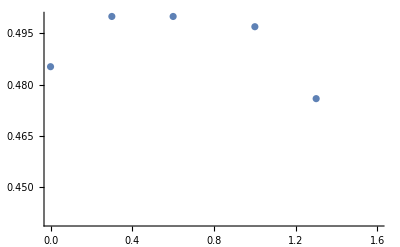

```mathematica
ListPlot[{{0,0.4852393705219679},{0.3,0.499893958571682},{0.6,0.49989048047301554},{1,0.49690248798550957},{1.3,0.47591848146145016},{1.6,0.40115622898223924}}]
```

#### α=π/6

```mathematica
α=π/6;
λ=0.1;
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0,0}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,1}]
Sum[s[p],{p,1,1}]/1
```

{-0.0000205201-0.361029 ⅈ}

-0.0000205201-0.361029 ⅈ

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0.3,0.3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
```

{-2.59105×10^-6-0.371985 ⅈ,-7.98827×10^-6-0.371895 ⅈ,2.22621×10^-6-0.371977 ⅈ,5.61046×10^-6-0.372029 ⅈ,1.62555×10^-6-0.372058 ⅈ,8.86851×10^-6-0.372036 ⅈ,-6.34463×10^-7-0.371145 ⅈ,-8.321×10^-6-0.37197 ⅈ,-7.20797×10^-6-0.371926 ⅈ,0.0000104148-0.371999 ⅈ,-7.13447×10^-6-0.372 ⅈ,-0.0000127876-0.37206 ⅈ,-0.0000150455-0.371989 ⅈ,9.87713×10^-6-0.371937 ⅈ,-3.27643×10^-6-0.372043 ⅈ,-0.0000123108-0.370893 ⅈ,9.28009×10^-6-0.372006 ⅈ,-0.000014619-0.371914 ⅈ,5.23731×10^-6-0.371929 ⅈ,-3.4385×10^-6-0.371855 ⅈ}

-2.11075×10^-6-0.371882 ⅈ

```mathematica
s1=-Im[%]
```

```mathematica
s1a=0.3701362024485271
```

0.370136

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0.6,0.6}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s03=-Im[%]
```

{-0.0000129576-0.371965 ⅈ,8.15704×10^-6-0.371991 ⅈ,1.10908×10^-6-0.371923 ⅈ,-0.000012317-0.369529 ⅈ,4.8504×10^-6-0.372018 ⅈ,-6.03506×10^-7-0.372012 ⅈ,1.67862×10^-6-0.372027 ⅈ,-7.41157×10^-6-0.37208 ⅈ,6.12726×10^-6-0.371527 ⅈ,-0.0000138204-0.371919 ⅈ,-0.0000119185-0.371974 ⅈ,-3.74574×10^-6-0.371766 ⅈ,5.00931×10^-6-0.371928 ⅈ,-6.87989×10^-6-0.371888 ⅈ,9.47043×10^-6-0.372008 ⅈ,-4.18624×10^-6-0.370839 ⅈ,4.55936×10^-6-0.371886 ⅈ,0.0000105126-0.372093 ⅈ,-8.25249×10^-6-0.372064 ⅈ,-0.0000127589-0.371944 ⅈ}

-2.16888×10^-6-0.371769 ⅈ

0.371769

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1,1}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s13=-Im[%]
```

{8.8467×10^-6-0.371323 ⅈ,3.04726×10^-6-0.3716 ⅈ,-8.09081×10^-6-0.370827 ⅈ,9.89448×10^-6-0.370366 ⅈ,-9.78949×10^-6-0.369809 ⅈ,-1.69176×10^-6-0.370531 ⅈ,-2.86625×10^-6-0.371758 ⅈ,0.0000105463-0.370747 ⅈ,9.86028×10^-6-0.371347 ⅈ,-5.57852×10^-6-0.371222 ⅈ,6.03687×10^-8-0.370986 ⅈ,-5.37079×10^-6-0.370258 ⅈ,-0.0000147654-0.371977 ⅈ,-0.0000109404-0.3626 ⅈ,-7.71071×10^-6-0.371739 ⅈ,-1.14527×10^-6-0.371634 ⅈ,0.0000103107-0.371588 ⅈ,6.56491×10^-6-0.370069 ⅈ,6.04301×10^-6-0.371605 ⅈ,3.74575×10^-6-0.369023 ⅈ}

4.85225×10^-8-0.37055 ⅈ

0.37055

```mathematica
s13a=0.3440957959346258
```

0.344096

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1.3,1.3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s17=-Im[%]
```

{-2.96941×10^-6-0.357093 ⅈ,-6.21099×10^-6-0.36196 ⅈ,-8.1976×10^-6-0.342406 ⅈ,-4.08415×10^-6-0.363581 ⅈ,-0.0000111229-0.36113 ⅈ,-6.2987×10^-6-0.358887 ⅈ,-8.93206×10^-6-0.357587 ⅈ,-7.34075×10^-6-0.359346 ⅈ,8.52044×10^-7-0.362137 ⅈ,-3.02126×10^-6-0.345157 ⅈ,-8.16111×10^-6-0.3418 ⅈ,-8.87462×10^-6-0.363624 ⅈ,-0.0000122642-0.363336 ⅈ,-4.8342×10^-6-0.351585 ⅈ,-0.000014099-0.362966 ⅈ,6.62771×10^-6-0.36367 ⅈ,-7.1858×10^-7-0.342904 ⅈ,-4.82514×10^-6-0.367107 ⅈ,-3.81235×10^-6-0.358048 ⅈ,5.97699×10^-6-0.358225 ⅈ}

-5.11551×10^-6-0.357127 ⅈ

0.357127

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1.6,1.6}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s2=-Im[%]
```

{6.34952×10^-6-0.343322 ⅈ,-0.0000108969-0.299809 ⅈ,1.30626×10^-6-0.303659 ⅈ,-2.83503×10^-6-0.313548 ⅈ,-4.09028×10^-6-0.306487 ⅈ,-0.0000111105-0.312857 ⅈ,-2.35088×10^-6-0.294 ⅈ,1.49124×10^-7-0.312604 ⅈ,-1.00134×10^-6-0.322604 ⅈ,-7.93142×10^-6-0.289959 ⅈ,8.3147×10^-6-0.281487 ⅈ,-2.30019×10^-6-0.288645 ⅈ,0.0000107214-0.312462 ⅈ,3.0932×10^-6-0.313348 ⅈ,9.40949×10^-7-0.298554 ⅈ,4.75247×10^-6-0.292142 ⅈ,0.0000101122-0.276369 ⅈ,-5.1233×10^-6-0.312074 ⅈ,-4.33012×10^-6-0.328976 ⅈ,2.20996×10^-6-0.315565 ⅈ}

-2.0101×10^-7-0.305923 ⅈ

0.305923

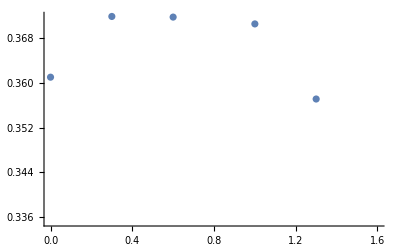

```mathematica
ListPlot[{{0,0.3610288692634736},{0.3,0.37188236027566224},{0.6,0.37176892015269747},{1,0.37055036666360874},{1.3,0.3571274186728712},{1.6,0.30592348490102966}}]
```

#### α=π/2

```mathematica
α=π/2;
λ=0.1;
```

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0,0}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,1}]
Sum[s[p],{p,1,1}]/1
```

{-9.09333×10^-6-0.167022 ⅈ}

-9.09333×10^-6-0.167022 ⅈ

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0.3,0.3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
```

{-7.53641×10^-7-0.172089 ⅈ,2.55104×10^-6-0.17217 ⅈ,-5.45249×10^-6-0.17208 ⅈ,2.26796×10^-6-0.171945 ⅈ,-7.48795×10^-7-0.172076 ⅈ,4.34618×10^-6-0.172039 ⅈ,3.96996×10^-6-0.17207 ⅈ,1.09258×10^-6-0.172045 ⅈ,-2.07902×10^-6-0.171923 ⅈ,-5.85134×10^-8-0.172084 ⅈ,1.86911×10^-6-0.17211 ⅈ,1.0821×10^-6-0.17186 ⅈ,2.29478×10^-6-0.171842 ⅈ,3.97092×10^-6-0.17209 ⅈ,-3.00547×10^-6-0.172073 ⅈ,1.11229×10^-6-0.172084 ⅈ,-2.69592×10^-7-0.171764 ⅈ,1.38035×10^-6-0.172142 ⅈ,-7.4341×10^-8-0.172125 ⅈ,-1.01355×10^-6-0.172105 ⅈ}

6.24093×10^-7-0.172036 ⅈ

```mathematica
s1=-Im[%]
```

```mathematica
s1a=0.3701362024485271
```

0.370136

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0.6,0.6}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s03=-Im[%]
```

{6.61343×10^-7-0.172034 ⅈ,2.59135×10^-6-0.172073 ⅈ,-5.40038×10^-6-0.171444 ⅈ,2.26617×10^-6-0.172099 ⅈ,-2.48757×10^-6-0.172092 ⅈ,1.34326×10^-6-0.172032 ⅈ,-2.15953×10^-6-0.171826 ⅈ,4.99029×10^-6-0.172101 ⅈ,1.46924×10^-6-0.172061 ⅈ,1.65702×10^-6-0.172098 ⅈ,-3.64885×10^-7-0.172019 ⅈ,-1.5643×10^-6-0.172095 ⅈ,4.92556×10^-6-0.172077 ⅈ,-4.84279×10^-7-0.172122 ⅈ,-6.28726×10^-6-0.171522 ⅈ,6.3885×10^-8-0.172091 ⅈ,-4.16037×10^-6-0.172047 ⅈ,2.34182×10^-6-0.172123 ⅈ,4.41719×10^-6-0.171918 ⅈ,2.48991×10^-6-0.172092 ⅈ}

3.15423×10^-7-0.171998 ⅈ

0.171998

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1,1}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s13=-Im[%]
```

{-1.69937×10^-6-0.171899 ⅈ,-4.10734×10^-6-0.170112 ⅈ,2.72356×10^-6-0.171883 ⅈ,-1.46643×10^-6-0.171766 ⅈ,-7.77456×10^-7-0.17171 ⅈ,-2.51502×10^-7-0.170897 ⅈ,4.40147×10^-6-0.171423 ⅈ,1.05708×10^-6-0.17096 ⅈ,1.12605×10^-6-0.170788 ⅈ,-5.78599×10^-6-0.172095 ⅈ,4.88379×10^-6-0.172063 ⅈ,-1.03469×10^-6-0.17057 ⅈ,3.82068×10^-6-0.166054 ⅈ,2.52021×10^-6-0.171754 ⅈ,-5.87358×10^-6-0.171895 ⅈ,2.36987×10^-6-0.172051 ⅈ,-1.54415×10^-6-0.171903 ⅈ,-4.65545×10^-7-0.171567 ⅈ,-6.07647×10^-6-0.171219 ⅈ,6.7714×10^-7-0.169572 ⅈ}

-2.75134×10^-7-0.171109 ⅈ

0.171109

```mathematica
s13a=0.3440957959346258
```

0.344096

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1.3,1.3}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s17=-Im[%]
```

{6.08698×10^-6-0.167302 ⅈ,-4.62738×10^-6-0.164321 ⅈ,8.59642×10^-7-0.164586 ⅈ,4.15584×10^-7-0.168241 ⅈ,4.89008×10^-6-0.159183 ⅈ,-3.14021×10^-6-0.159764 ⅈ,1.55641×10^-6-0.1651 ⅈ,-2.43564×10^-6-0.171324 ⅈ,5.3977×10^-6-0.163694 ⅈ,-5.85824×10^-6-0.160849 ⅈ,-4.52198×10^-6-0.16386 ⅈ,2.78405×10^-6-0.162086 ⅈ,-5.00584×10^-6-0.166735 ⅈ,3.5434×10^-6-0.161109 ⅈ,-5.81205×10^-6-0.155371 ⅈ,-5.1569×10^-6-0.164646 ⅈ,-2.70303×10^-6-0.162365 ⅈ,-3.98046×10^-6-0.167954 ⅈ,2.23504×10^-6-0.165863 ⅈ,2.81001×10^-6-0.161952 ⅈ}

-6.33141×10^-7-0.163815 ⅈ

0.163815

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-1.6,1.6}],{i,0,Nx-1},{j,0,Ny-1}];M1B=MatrixExp[-I π/2 H5].MatrixExp[-I π/2 H4[ Bi]].MatrixExp[-I π/2 H3[Bi]]. MatrixExp[-I π/2 H2[Bi]].MatrixExp[-I π/2 H1[Bi]];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M=1/(E^(α/2)+E^(-α/2))(Id E^(α/2)+(Id-Pr)E^(-α/2)+E^(-α/2) Pr.MatrixPower[M10,n].MatrixPower[M1B,n]);s[p]=(Det[M]-1)/(Bi (Nx  thickness)n)//N,{p,1,20}]
Sum[s[p],{p,1,20}]/20
s2=-Im[%]
```

{3.04765×10^-6-0.15232 ⅈ,3.04816×10^-6-0.126062 ⅈ,5.61836×10^-6-0.128967 ⅈ,1.59566×10^-6-0.152643 ⅈ,-3.02916×10^-6-0.150814 ⅈ,-5.84767×10^-6-0.158521 ⅈ,1.45526×10^-6-0.132192 ⅈ,-2.16822×10^-6-0.133941 ⅈ,1.64983×10^-6-0.153109 ⅈ,3.9894×10^-6-0.139696 ⅈ,-4.96454×10^-7-0.141266 ⅈ,5.05979×10^-6-0.14105 ⅈ,-4.90697×10^-6-0.156098 ⅈ,2.5818×10^-6-0.140056 ⅈ,4.92986×10^-8-0.151116 ⅈ,4.30471×10^-6-0.130588 ⅈ,-1.43066×10^-6-0.15205 ⅈ,5.05051×10^-6-0.149565 ⅈ,3.28947×10^-6-0.138598 ⅈ,4.17927×10^-6-0.155243 ⅈ}

1.352×10^-6-0.144195 ⅈ

0.144195

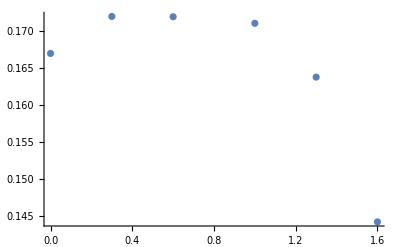

```mathematica
ListPlot[{{0,0.16702220451775862},{0.3,0.17203582488565203},{0.6,0.17199837871685902},{1,0.1711090543596866},{1.3,0.16381530200207728},{1.6,0.14419477197106337}}]
```

## Localization, Nx=20, Ny=40, λ=0.1

```mathematica
state[x_,y_]=Table[If[i==Ny Mod[x,Nx]+Mod[y,Ny],1,0],{i,0,Nx Ny-1}];
```

```mathematica
Table[w[i,j]=.,{i,0,Nx-1},{j,0,Ny-1}];
```

```mathematica
Table[Table[w[i,j]= RandomReal[{-0.6,0.6}],{i,0,Nx-1},{j,0,Ny-1}];M10=MatrixExp[I π/2 H1[0]].MatrixExp[I π/2 H2[0]]. MatrixExp[I π/2 H3[0]].MatrixExp[I π/2 H4[0]].MatrixExp[I π/2 H5];M11[p]=MatrixPower[M10,n];,{p,1,20}];
```

```mathematica
y=Ny/2;
loc=Table[Max[Table[(((state[0+i-1,y+j-1].M11[p].state[0,y])/(state[0,y].M11[p].state[0,y]))//Abs),{p,1,20}]],{i,1,Nx/2},{j,1,Ny-y}];
%//MatrixForm
ListPlot[Table[loc[[i,1]],{i,1,Nx/2}],PlotRange->5,PlotLegends->LineLegend[{"x direction"}],PlotStyle->PointSize[1],AxesStyle->Thick,LabelStyle->{FontSize->25,FontWeight->"Bold",Gray,FontFamily->"LM Roman 10"}]
ListPlot[Table[loc[[1,i]],{i,1,Ny-y}],PlotRange->5,PlotLegends->LineLegend[{"y direction"}],PlotStyle->PointSize[Large],AxesStyle->Thick,LabelStyle->{FontSize->25,FontWeight->"Bold",Gray,FontFamily->"LM Roman 10"}]
```

(1. | 0.46775 | 1.21774 | 0.272668 | 0.184625 | 0.10224 | 0.278937 | 0.139658 | 0.0466304 | 0.0155756 | 0.314613 | 0.00170011 | 0.0257852 | 0.0220813 | 0.0407355 | 0.000292742 | 0.000410578 | 0.000404692 | 0.00085973 | 0.000766184
1.57975 | 0.805749 | 0.452436 | 0.526822 | 0.249545 | 0.250957 | 0.112497 | 0.112501 | 0.0792019 | 0.0175816 | 0.0987136 | 0.155907 | 0.00844942 | 0.0068839 | 0.00545859 | 0.012416 | 0.000712246 | 0.00237701 | 0.000588826 | 0.00162355
0.850113 | 0.376528 | 0.595024 | 0.34667 | 0.171494 | 0.149724 | 0.26609 | 0.0659229 | 0.0651072 | 0.120486 | 0.091978 | 0.0083389 | 0.0249423 | 0.0116693 | 0.0186797 | 0.00334814 | 0.0222033 | 0.000304396 | 0.000233345 | 0.000747373
0.667102 | 0.727157 | 0.367819 | 0.256143 | 0.156118 | 0.129107 | 0.047225 | 0.151085 | 0.00740769 | 0.0200686 | 0.516178 | 0.0958993 | 0.0055731 | 0.00578212 | 0.033444 | 0.00754447 | 0.0015471 | 0.00067627 | 0.00124339 | 0.00158429
0.8782 | 0.277932 | 0.402869 | 0.138398 | 0.229576 | 0.112089 | 0.0438701 | 0.117473 | 0.026055 | 0.0245243 | 0.00497082 | 0.00649364 | 0.00241129 | 0.00285247 | 0.00507768 | 0.015518 | 0.00261498 | 0.000262379 | 0.000147969 | 0.000773075
0.305088 | 0.159478 | 0.162333 | 0.201257 | 0.0978268 | 0.104516 | 0.0120273 | 0.0293939 | 0.00773816 | 0.0328431 | 0.00742007 | 0.00304118 | 0.00551947 | 0.00297368 | 0.00125462 | 0.00103833 | 0.000698693 | 0.000197691 | 0.000133819 | 0.000990653
0.0344984 | 0.167148 | 0.0369326 | 0.110095 | 0.166923 | 0.111359 | 0.366828 | 0.133895 | 0.0444638 | 0.00229354 | 0.00220513 | 0.00843917 | 0.0105673 | 0.0039186 | 0.000855239 | 0.000895054 | 0.000645741 | 0.000260673 | 0.000351224 | 0.00100378
0.138263 | 0.0135333 | 0.103632 | 0.0356432 | 0.194799 | 0.0603358 | 0.0824613 | 0.362189 | 0.0051422 | 0.0273518 | 0.00591335 | 0.00862485 | 0.00184899 | 0.00119142 | 0.000229102 | 0.00111263 | 0.000609487 | 0.00209879 | 0.00187307 | 0.000462546
0.0325555 | 0.0124445 | 0.0229882 | 0.0211977 | 0.00958161 | 0.06328 | 0.0580962 | 0.123822 | 0.0151213 | 0.0110298 | 0.0147709 | 0.00129409 | 0.00371014 | 0.000632087 | 0.00104649 | 0.00151465 | 0.0026145 | 0.000955748 | 0.000440783 | 0.000855277
0.0140708 | 0.024532 | 0.0202726 | 0.0401488 | 0.0160917 | 0.0170472 | 0.0407406 | 0.0178793 | 0.0182964 | 0.0378662 | 0.0397316 | 0.101471 | 0.00223478 | 0.0100039 | 0.00071714 | 0.00160088 | 0.00390831 | 0.00338676 | 0.0015616 | 0.000402498)

with W=0.6

```mathematica
loc=({{1.0000000000000002, 0.4677504060715428, 1.2177387223991423, 0.2726684916544055, 0.1846253931613238, 0.10223996450093144, 0.27893717133813245, 0.1396578209233193, 0.04663036096653832, 0.01557559330946126, 0.31461275638335157, 0.0017001067508611758, 0.02578521633170481, 0.022081268745420813, 0.04073551533364039, 0.000292742362974547, 0.00041057755163756047, 0.0004046922064428058, 0.0008597297419332709, 0.0007661837381281356}, {1.579749952964544, 0.8057492105716566, 0.4524355762697074, 0.5268219163674355, 0.24954504413971879, 0.2509565602711455, 0.11249666499171586, 0.11250137782044832, 0.07920194411273199, 0.017581632027787, 0.09871358484703155, 0.15590710597923046, 0.008449419126477332, 0.006883899624227874, 0.005458585571891193, 0.012416031192491371, 0.0007122459438848478, 0.0023770119758283626, 0.0005888263122509143, 0.0016235478282473504}, {0.8501133683028094, 0.3765284187951169, 0.5950241081174492, 0.34666952637845744, 0.17149420565944368, 0.14972372247472404, 0.26609004983668383, 0.06592287905740847, 0.06510722327313485, 0.12048558979648044, 0.09197802370372019, 0.008338902741187301, 0.02494229008362269, 0.011669331655046666, 0.018679715452521273, 0.0033481368176763097, 0.022203260030720318, 0.00030439605345813654, 0.0002333448499064201, 0.0007473726665884405}, {0.6671017967421533, 0.7271574771096967, 0.36781941121252415, 0.25614253054439806, 0.15611786537400862, 0.12910679776273865, 0.04722501434951004, 0.151085436083441, 0.007407687779463848, 0.02006857170076138, 0.5161779234812391, 0.095899291970697, 0.005573103686086788, 0.0057821159767570685, 0.03344398005472001, 0.007544473002536041, 0.0015470966592656262, 0.000676269597769804, 0.0012433881782286103, 0.0015842864044545025}, {0.878199592793002, 0.277931615780123, 0.4028689226288859, 0.1383977101416881, 0.22957615907135429, 0.1120893042851728, 0.04387008404810966, 0.11747255202945699, 0.026054972910764865, 0.024524318919400986, 0.004970821561550335, 0.006493642165930244, 0.0024112939101918387, 0.002852465184685999, 0.005077681895943264, 0.015518041413356314, 0.0026149819893666933, 0.0002623794470947892, 0.00014796878144728888, 0.0007730752554797008}, {0.30508785981110875, 0.1594779368909682, 0.162332731734405, 0.20125717868005438, 0.09782684775957977, 0.10451624395986646, 0.012027349172459916, 0.029393884361724503, 0.00773816487932634, 0.03284309236367555, 0.007420066314748701, 0.003041183584015993, 0.005519471540208549, 0.002973678152419341, 0.0012546176980450948, 0.0010383315100154107, 0.0006986930774214756, 0.0001976912371921632, 0.0001338185376797453, 0.0009906528238447251}, {0.03449840746070131, 0.16714756800345149, 0.036932570872404265, 0.11009496206921573, 0.16692319084835483, 0.11135926457724546, 0.3668281140134877, 0.13389508392647473, 0.044463750556052145, 0.0022935413229301246, 0.0022051334544387945, 0.008439172745699318, 0.010567319760470522, 0.0039186016042976335, 0.0008552386464509922, 0.0008950536379590982, 0.0006457408745391572, 0.0002606733704266722, 0.0003512236960853959, 0.0010037768890074547}, {0.1382627520547323, 0.013533265036109056, 0.1036316099974985, 0.035643179266359404, 0.19479897688609843, 0.06033575562836093, 0.08246132494634661, 0.362188806952002, 0.005142201149986023, 0.027351763731072124, 0.005913349401650496, 0.00862485347783682, 0.001848991079743977, 0.0011914152400523922, 0.00022910179225251587, 0.0011126318976258207, 0.000609487145367093, 0.0020987888378150563, 0.0018730674296865459, 0.00046254584861369594}, {0.03255548487774284, 0.012444542423397447, 0.022988166685384028, 0.02119765735626045, 0.009581609750086484, 0.06327997566365205, 0.058096209171947626, 0.12382231879593195, 0.015121337416765886, 0.011029754250721033, 0.014770902691920232, 0.00129409283505623, 0.003710135713681393, 0.0006320867546983868, 0.0010464900105762024, 0.0015146476815962031, 0.0026144953959367587, 0.0009557482456183345, 0.00044078346871754447, 0.0008552767839959854}, {0.014070831017736837, 0.024531980264424012, 0.020272639799265975, 0.04014875103288378, 0.016091703012360185, 0.01704721831869577, 0.04074060797729003, 0.017879328168705966, 0.01829636790885991, 0.037866173565029915, 0.03973161719583005, 0.1014710857956699, 0.002234776222934384, 0.010003895871717502, 0.0007171397409249205, 0.0016008792796822291, 0.003908305565778701, 0.003386757199572877, 0.0015615974887927156, 0.00040249752469004676}});
```

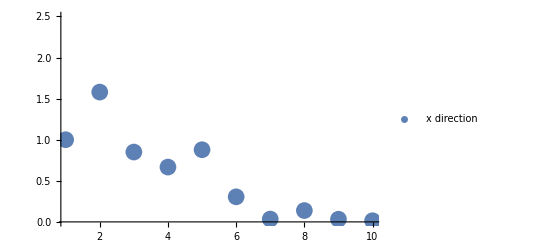

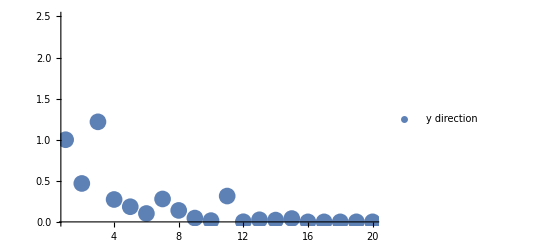

```mathematica
ListPlot[Table[loc[[i,1]],{i,1,Nx/2}],PlotRange->2.5,PlotLegends->LineLegend[{"x direction"}],PlotStyle->PointSize[0.03],AxesStyle->Thick,LabelStyle->{FontSize->25,FontWeight->"Bold",GrayLevel[.35],FontFamily->"LM Roman 10"}]
ListPlot[Table[loc[[1,i]],{i,1,Ny-Ny/2}],PlotRange->2.5,PlotLegends->LineLegend[{"y direction"}],PlotStyle->PointSize[0.03],AxesStyle->Thick,LabelStyle->{FontSize->25,FontWeight->"Bold",GrayLevel[.35],FontFamily->"LM Roman 10"}]
```

with W=0.3

```mathematica
loc=({{1., 0.7445677187126123, 1.7870167762792386, 0.6703516401644373, 0.6487562040098953, 0.5386375681972152, 0.3115654666981248, 0.038704397679334805, 0.03886066616388861, 0.015556533403967364, 0.020443618454903226, 0.004910279895118102, 0.00644433306249244, 0.0030161353367764944, 0.010907147918745506, 0.0015804001686512612, 0.001375572439884234, 0.0014986337917350895, 0.004164405867633175, 0.00022090707381804174}, {1.6317220872538596, 1.1226813713991268, 0.7245062967703992, 0.9719074654516727, 0.5704338458578082, 0.39273341007967494, 0.049130879108371196, 0.14250574081483958, 0.028775562935880076, 0.07869386640772084, 0.004033439215054992, 0.02714882394496685, 0.0029652165947781934, 0.002301134597309833, 0.020669526286123136, 0.012041596330123515, 0.0025275891290600164, 0.0003414471519170224, 0.0010564426799610904, 0.0005721268933939427}, {1.8853915501045595, 0.672567025128869, 0.4973457162906016, 1.480280120590568, 0.3313723625181065, 0.08674695518367434, 0.12567015388188052, 0.07623632394307206, 0.05678895786216137, 0.013081832193107903, 0.03452328545619591, 0.005002045126390274, 0.014408635064775284, 0.012697643805239271, 0.050296650358355816, 0.0015626977100983961, 0.001431770593148338, 0.0038596187363933113, 0.00024981464180701585, 0.00023155382351816876}, {1.0225064602426441, 0.6562484845126737, 0.6923550236868968, 0.5909101188438115, 0.16501194576207331, 0.30504462842459185, 0.06496513341740705, 0.20897733193942233, 0.11308513609211264, 0.014227413533231204, 0.016166654133179054, 0.03334873381067406, 0.009871401092175387, 0.01080528947334631, 0.011208174246202341, 0.009416748178730719, 0.000603146492234745, 0.0033057619058182376, 0.00040895113743290166, 0.0005749268002525349}, {0.9749772775800858, 0.501470146678923, 0.3113234806074513, 0.2501821173348843, 0.789207378318766, 0.21591823949410685, 0.318042957837453, 0.13147069993238655, 0.11788549385628551, 0.014456801596880777, 0.012379124169385821, 0.012136751791768968, 0.009921342511847264, 0.041408454366073336, 0.042790352205664996, 0.0015610727994567533, 0.012207639038199434, 0.0005481839201588076, 0.0008506088606129881, 0.00025301686678116546}, {0.692242168455481, 1.1113394751794818, 0.23695474245972203, 0.31494479283660587, 0.8868772200293406, 0.8355332407989841, 0.28810840634755797, 0.43809279038547483, 0.028491175957876546, 0.1577619958814721, 0.01186561610064152, 0.009394004175326851, 0.028850019366298614, 0.09861168554088007, 0.005823963718674415, 0.019622237054522235, 0.0008531699843050949, 0.0009933265336273826, 0.0015538582999436602, 0.0017337872074929686}, {0.7703744670943804, 0.25037126421782263, 0.17327560133247744, 0.03886201715481315, 0.11177345835595238, 0.6446685908905635, 0.14466527502575532, 0.07463729706004972, 0.009523052176461929, 0.038479204662425076, 0.016235825309078248, 0.015863619619880677, 0.032364998132149575, 0.062073385904691365, 0.012469979825377933, 0.00637163310742164, 0.011760669959525873, 0.0009926045851430846, 0.004228662749169506, 0.000331975539634575}, {0.9112409657313036, 0.18292739980422848, 0.2974673496303047, 0.08985215417230256, 0.23759082544474636, 0.11758898095251678, 0.04647175131285345, 0.03811474328979922, 0.0488809237588089, 0.024023310385871403, 0.020326371535612238, 0.005190686745190275, 0.015073625841634831, 0.002800724666796281, 0.0030694242271410137, 0.0008015620560834506, 0.005193832428533019, 0.0037402439041385794, 0.0005659128257868805, 0.0005001845137308855}, {0.4305721326071033, 0.07351110760156573, 0.029098487492441098, 0.03706210613237687, 0.08122689101551873, 0.0705156214567074, 0.04893364591603215, 0.015609743984970219, 0.0086504564182962, 0.010355114149127768, 0.026024880702681767, 0.006904333845709595, 0.0020501715961173056, 0.012124716819499618, 0.0019638722252974306, 0.0024713437792363534, 0.001940098980359372, 0.0018339546039848012, 0.00042985431797594784, 0.0003090390093821821}, {0.11178300524101287, 0.057208703894741364, 0.10414192885925443, 0.02332298957803105, 0.12004256397569954, 0.013084065221414934, 0.033540993463037336, 0.04098957831620154, 0.012324613943084742, 0.007409236619316788, 0.0017292231846834586, 0.0045650522316185715, 0.0017689372559756885, 0.0008254012621409943, 0.002479638514540162, 0.0007219907677383815, 0.0011038323595710003, 0.0002922543463349136, 0.00016036394021825523, 0.00016352999736700893}});
```

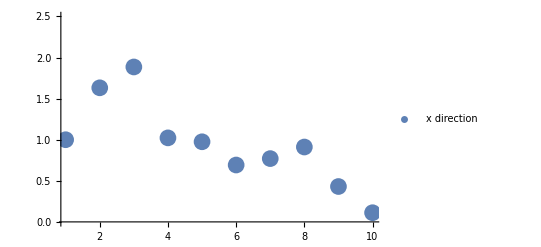

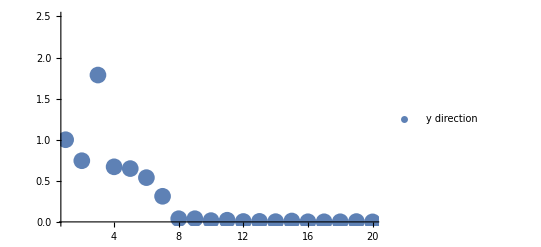

```mathematica
ListPlot[Table[loc[[i,1]],{i,1,Nx/2}],PlotRange->2.5,PlotLegends->LineLegend[{"x direction"}],PlotStyle->PointSize[0.03],AxesStyle->Thick,LabelStyle->{FontSize->25,FontWeight->"Bold",GrayLevel[.35],FontFamily->"LM Roman 10"}]
ListPlot[Table[loc[[1,i]],{i,1,Ny-Ny/2}],PlotRange->2.5,PlotLegends->LineLegend[{"y direction"}],PlotStyle->PointSize[0.03],AxesStyle->Thick,LabelStyle->{FontSize->25,FontWeight->"Bold",GrayLevel[.35],FontFamily->"LM Roman 10"}]
```

with W=0

```mathematica
loc=({{1., 0.6074604310815868, 0.7240415689781088, 0.44356550148885543, 0.1561532124562053, 0.11213150057140706, 0.9652571848687687, 0.03624828567883904, 0.20679803098783575, 0.4443254653136639, 1.0646604786507703, 0.6582568235845748, 0.48546906485023733, 0.20770850021143727, 1.2456099424513325, 0.22889329974841188, 0.1730673039592862, 0.251480979362033, 0.8989909659294418, 0.11889689555781201}, {0.6216830506772003, 0.6040161170519731, 0.10294637829923184, 0.42600170692357225, 0.26066002802855814, 0.33891600789347637, 0.2797127730816382, 1.0560337033439875, 0.20187419245462887, 0.8067262096129623, 0.566483185745495, 1.072982854385838, 0.4220647360982293, 0.6702754330283439, 0.06959143949543144, 0.5763271429189231, 0.42221007738319727, 0.6365143021904374, 0.29795038684086145, 0.8667336199088336}, {2.115772790284724, 0.40218509547258835, 1.4255267474424793, 0.22676106186178846, 0.46369418708481125, 0.4908092255215712, 0.36269058873178994, 0.13948407189700165, 0.3733871979230436, 0.255442892449096, 0.6755110920374329, 0.4921153161303541, 0.36712280363643696, 0.062137202711079954, 0.26082734013227604, 0.48399901202618323, 0.8581974008913129, 0.5176859809928009, 0.5761057851577704, 0.06234313335630899}, {0.24507676731814096, 0.681047268016124, 0.4934964079230292, 0.7424095934371912, 0.045954045180708364, 0.10114890568174742, 0.18570761476861522, 0.1963428142633956, 0.31020861750340095, 0.24503996302718692, 0.5476208630858802, 1.6332152361819527, 0.11530473774813767, 0.5844446301630353, 0.19422812687401944, 0.3055793827229352, 0.6287539780595384, 1.4635694649815365, 0.5447777106231744, 0.8832093343336621}, {0.6631921171904839, 0.3092327407063866, 0.5235420209660298, 0.6262533770087783, 1.1440889333406183, 0.07410369017069544, 1.23940994677895, 0.6048599272453381, 0.7166044043245788, 0.4431968436003255, 0.9909360633569181, 0.6553638675239852, 0.6631975378886816, 0.25113740650526123, 0.654653693085346, 0.4645016911766273, 0.9138837607944468, 0.39693427750569305, 0.5166350405703455, 0.09503919801055127}, {0.3012728116650327, 0.2975738106911473, 0.37185884719583634, 0.28603444752047835, 0.42881672268726817, 1.4181977479147838, 0.2928090583617504, 0.5423062910302007, 0.3598248990430305, 0.778965949390027, 0.2955746933145097, 0.7163696512138151, 0.3991926585724944, 0.34520016179442287, 0.18823313413554452, 1.432700135208107, 0.45152057925215366, 1.0617053157338199, 0.20284509716978588, 0.44426395636407673}, {0.6298218366668559, 0.23094529602117708, 0.6778757956373548, 0.29974862580584516, 0.6891758940677515, 0.17878698403844562, 1.3385567693721443, 0.7629298612445592, 1.0154824604544936, 0.16181017492327154, 0.5568226330236976, 0.46143977199551073, 0.15092791305570394, 0.5527112843828418, 0.4941092689143667, 0.35213441410620816, 0.48890968949043506, 0.2859537429283188, 0.3092197072564369, 0.04565326349863224}, {0.3011831632221486, 0.7464023442755746, 0.2771625485394893, 0.6589049771708464, 0.26874231077228794, 0.8770482600628468, 0.2683028237063475, 1.1987451801576419, 0.037696091278027366, 0.43818562006337836, 0.08755664904756745, 0.9898159867461789, 0.7385178500436714, 0.7725179607760482, 0.2690846330272709, 1.5312259555759438, 0.4233061407085767, 1.2908934700708197, 0.08053894936671074, 0.698949050654875}, {2.4025445506243486, 0.1357718805832904, 0.3087255818781812, 0.1526945309829923, 1.0762752355939271, 0.06604938894289976, 0.6873079264077628, 0.4366446581964105, 0.4023079634297224, 0.6621274654358912, 0.14500406323427323, 0.29351471761044884, 0.49046152217281036, 0.37592359851607243, 1.4163837562804247, 0.38898804551028265, 0.5943466335930155, 0.513733074627911, 0.6197977400982799, 0.09247426174724716}, {0.7960491626447234, 0.5010981937190446, 0.15630256858768654, 0.5584600851032754, 0.08209922144662865, 0.7476218042900151, 0.6244364788023435, 0.4908260686469842, 0.7653557383983557, 1.2520665013696597, 0.4013158375767293, 0.2139529188658127, 0.04279734652280532, 0.6362687923471038, 0.13356635764394423, 0.7145409521031842, 0.6914999298135653, 0.798673724767032, 0.3226907348844258, 0.202742872254365}});
```

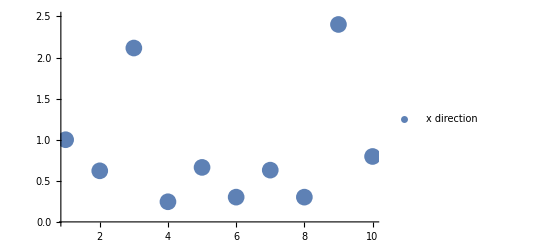

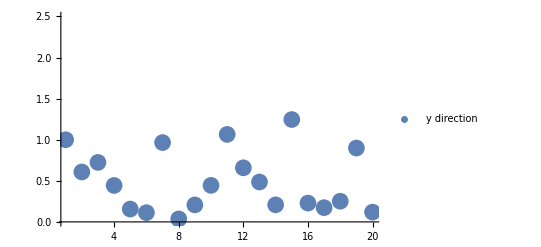

```mathematica
ListPlot[Table[loc[[i,1]],{i,1,Nx/2}],PlotRange->2.5,PlotLegends->LineLegend[{"x direction"}],PlotStyle->PointSize[0.03],AxesStyle->Thick,LabelStyle->{FontSize->25,FontWeight->"Bold",GrayLevel[.35],FontFamily->"LM Roman 10"}]
ListPlot[Table[loc[[1,i]],{i,1,Ny-Ny/2}],PlotRange->2.5,PlotLegends->LineLegend[{"y direction"}],PlotStyle->PointSize[0.03],AxesStyle->Thick,LabelStyle->{FontSize->25,FontWeight->"Bold",GrayLevel[.35],FontFamily->"LM Roman 10"}]
```

## Summary

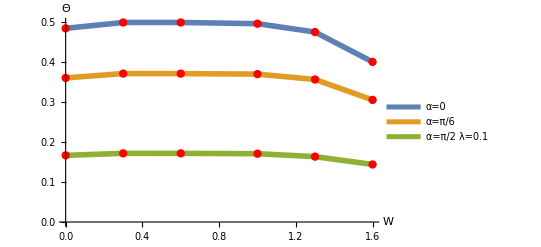

```mathematica
plot1=ListPlot[{{{0,0.4852393705219679},{0.3,0.499893958571682},{0.6,0.49989048047301554},{1,0.49690248798550957},{1.3,0.47591848146145016},{1.6,0.40115622898223924}},{{0,0.3610288692634736},{0.3,0.37188236027566224},{0.6,0.37176892015269747},{1,0.37055036666360874},{1.3,0.3571274186728712},{1.6,0.30592348490102966}},{{0,0.16702220451775862},{0.3,0.17203582488565203},{0.6,0.17199837871685902},{1,0.1711090543596866},{1.3,0.16381530200207728},{1.6,0.14419477197106337}}},Joined->{True,True,True,True,True},PlotStyle->{Thickness[0.01],Thickness[0.01],Thickness[0.01],Dashed,Dashed,Dashed},PlotLegends->LineLegend[{"α=0","α=π/6","α=π/2 λ=0.1"}],AxesLabel->{"W","Θ"},PlotRange->{0,0.5},LabelStyle->{FontSize->25,(*FontWeight->"Bold",*)GrayLevel[.15],FontFamily->"LM Roman 10"},AxesStyle->Thick,Mesh->All,MeshStyle->Directive[PointSize[Large],Red]]
```

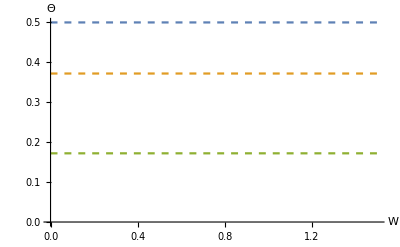

```mathematica
plot2=ListPlot[{Table[{1.5/20 n,0.5},{n,0,20}],Table[{1.5/20 n,0.37201110537715776},{n,0,20}],Table[{1.5/20 n,0.1721028986836638},{n,0,20}]},Joined->{True,True,True,True,True},PlotStyle->{Dashed,Dashed,Dashed},AxesLabel->{"W","Θ"},PlotRange->{0,0.5},LabelStyle->{FontSize->25,(*FontWeight->"Bold",*)GrayLevel[.15],FontFamily->"LM Roman 10"},AxesStyle->Thick]
```

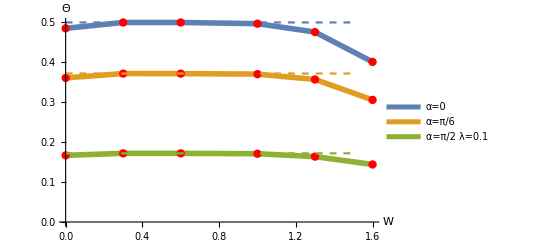

```mathematica
plot=Show[plot1,plot2]
```

```mathematica
Export["prova1.eps",plot]
```

prova1.eps

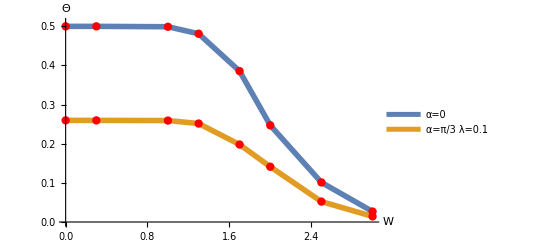

```mathematica
plot3=ListPlot[{{{0,0.5},{0.3,0.49999280391359796},{1,0.49897266536987595},{1.3,0.48110840053714815},{1.7,0.3856111589029572},{2,0.2471495887755022},{2.5,0.1011762112242147},{3,0.02676224398527608}},{{0,0.25976361091989103},{0.3,0.25968744711606145},{1,0.2592715233139963},{1.3,0.2516513965790576},{1.7,0.19797365318528562},{2,0.14126280061004318},{2.5,0.05217346333835901},{3,0.01431283694396155}}},Joined->{True,True},PlotStyle->{Thickness[0.01],Thickness[0.01]},PlotLegends->LineLegend[{"α=0","α=π/3 λ=0.1"}],AxesLabel->{"W","Θ"},PlotRange->{0,0.51},LabelStyle->{FontSize->25,(*FontWeight->"Bold",*)GrayLevel[.15],FontFamily->"LM Roman 10"},AxesStyle->Thick,Mesh->All,MeshStyle->Directive[PointSize[Large],Red]]
```

```mathematica
Export["prova2.eps",plot3]
```

prova2.eps